```mathematica
(*
constant young utility case
*)
```

```mathematica
Clear[eq]
eq[D_,alpha_,beta_,sigma_,x_]:=(2*alpha*x*(beta-D)*(1-sigma^2))-(beta-2*D+Sqrt[(beta-2*D)^2+4*(1-sigma^2)*D*(beta-D)])
Simplify[Solve[eq[D,alpha,beta,sigma,x]==0,{D}]]
```

{{D→beta},{D→(alpha beta x (1+alpha (-1+sigma^2) x))/(-1+2 alpha x+alpha^2 (-1+sigma^2) x^2)}}

```mathematica
Clear[eq]
eq[D_,alpha_,beta_,sigma_,x_]:=(2*alpha*x*(beta-D)*(1-sigma^2))-(beta-2*D+Sqrt[(beta-2*D)^2+4*(1-sigma^2)*D*(beta-D)])
Simplify[Solve[eq[D,0.35,0.495,0.4,10/3]==0,{D}]]
```

{{D→0.0607895},{D→0.495}}

```mathematica
Clear[eq]
eq[D_,alpha_,beta_,sigma_,x_]:=(2*alpha*x*(beta-D)*(1-sigma^2))-(beta-2*D+Sqrt[(beta-2*D)^2+4*(1-sigma^2)*D*(beta-D)])
Simplify[Solve[eq[D,0.35,0.495,sigma,10/3]==0,{D}]]
```

{{D→(0.0707143-0.565714 sigma^2+0.495 sigma^4)/(0.0204082-1.02041 sigma^2+1. sigma^4)},{D→0.495}}

```mathematica
{{D->(0.0707142857142857-0.5657142857142856 sigma^2+0.49499999999999994 sigma^4)/(0.02040816326530612-1.0204081632653061 sigma^2+1. sigma^4)},{D->0.49499999999999994}}
```

```mathematica
Clear[Debt]
Debt[sigma_]:=(0.0707142857142857-0.5657142857142856 sigma^2+0.49499999999999994 sigma^4)/(0.02040816326530612-1.0204081632653061 sigma^2+1. sigma^4)
```

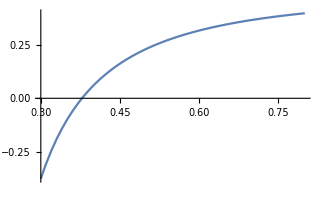

```mathematica
Plot[Debt[sigma],{sigma,0.3,0.8}]
```

```mathematica
Clear[Debt]
Clear[Debtab]
Debt[alpha_,beta_,x_,sigma_]:=(alpha beta x (1+alpha (-1+sigma^2) x))/(-1+2 alpha x+alpha^2 (-1+sigma^2) x^2)
Debtab[x_,sigma_]:=Debt[0.35,0.495,x,sigma]
```

```mathematica
Plot3D[Debtab[x,y],{x,3,5},{y,0,1},Filling->Bottom,RegionFunction->Function[{x,y,z},0<z<0.495],AxesLabel->{x,σ,Debt},ColorFunction->"DarkRainbow"]
```

-Graphics3D-

```mathematica
(*Testing, result agrees with simulation result*)
Debtab[10/3,0.4]
```

0.0607895

```mathematica
(*Testing result for riskless & hightech case*)
Clear[Rf]
Rf[alpha_,beta_,x_,sigma_,D_]:=(2*alpha*x*(beta-D)*(1-sigma^2))/(beta-2*D+Sqrt[(beta-2*D)^2+4*(1-sigma^2)*D*(beta-D)])
Rf[0.35,0.495,4.5,0.5,0.001]
```

1.18185

```mathematica
(*
log utility case
*)
```

```mathematica
Clear[eq]
eq[D_,alpha_,beta_,sigma_,x_,Y_]:=(2*alpha*x*(beta-D)*(1-sigma^2)*Y)-(beta-2*D+Sqrt[(beta-2*D)^2+4*(1-sigma^2)*D*(beta-D)])
Simplify[Solve[eq[D,alpha,beta,sigma,x,Y]==0,{D}]]
```

{{D→beta},{D→(alpha beta x Y (1+alpha (-1+sigma^2) x Y))/(-1+2 alpha x Y+alpha^2 (-1+sigma^2) x^2 Y^2)}}

```mathematica
Plot3D[Debtab[x,y],{x,2,12},{y,0.2,1},Filling->Bottom,RegionFunction->Function[{x,y,z},0<z&&(12-x)^2/8.5^2+(y-0.2)^2/0.55^2>1],AxesLabel->{"xY_(t - 1)",σ,"Debt-to-income ratio"},ColorFunction->"DarkRainbow"]
```